```mathematica
model = a*x^b +c ;
```

```mathematica
TRAPEZIO
```

TRAPEZIO

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_trapezio.txt","Table"];
Trapezio = Take[data][[All,{1,3}]];
DELTATrapezio = Take[data][[All,{2,4}]];
```

```mathematica
linetrap=FindFit[DELTATrapezio, model,{a,b,c},x]
```

{a→0.0288749,b→1.9506,c→9.74495×10^-7}

```mathematica
SIMPSON
```

SIMPSON

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_simpson.txt","Table"];
Simpson= Take[data][[All,{1,3}]];
DELTASimpson= Take[data][[All,{2,4}]];
```

```mathematica
linesimp=FindFit[DELTASimpson, model,{a,b,c},x,MaxIterations->1000]
```

{a→112.267612700022770349345894862175486306249,b→5.07133541200735149432442743611952367795526,c→1.29051757700435793263028295505682054519367×10^-6}

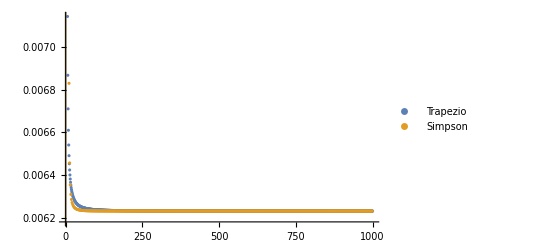

```mathematica
Show[{ListPlot[{Trapezio,Simpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->All],Plot[{model/.linetrap,model/.linesimp},{x,0,1},PlotStyle->Opacity[0.4]]}]
```

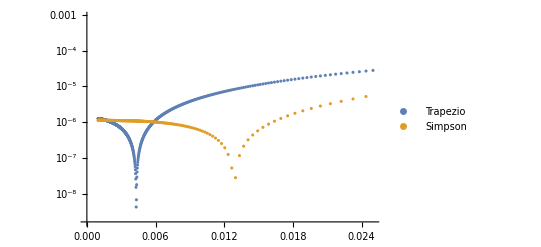

```mathematica
ListLogPlot[{DELTATrapezio,DELTASimpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->{{0,0.025},Automatic}]
```

```mathematica
HERMITE
```

HERMITE

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_hermite.txt","Table"];
DELTAHermite = Take[data][[All,{1,3}]]
```

{{2,0.005131886161429156066604573283029822050593793392181},{4,0.00391067501960266558636014622152288211509585380554},{5,0.008092154898845103222493335692888649646192789077759},{8,0.002539493358377102171646866324294933292549103498459},{100,0.0002616410539777678503567392986894901696359738707542}}

```mathematica
LAGUERRE
```

LAGUERRE

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_laguerre.txt","Table"];
DELTALaguerre = Take[data][[All,{1,3}]]
```

{{2,3.028142786434123712169252939929720014333724975586×10^-19},{3,1.431909197333394723194999187398934736847877502441×10^-18},{4,1.431909197333394723194999187398934736847877502441×10^-18},{5,5.645474593449911759890369467029813677072525024414×10^-19},{6,5.645474593449911759890369467029813677072525024414×10^-19},{7,5.645474593449911759890369467029813677072525024414×10^-19},{8,5.645474593449911759890369467029813677072525024414×10^-19},{9,3.028142786434123712169252939929720014333724975586×10^-19},{10,5.645474593449911759890369467029813677072525024414×10^-19},{12,5.645474593449911759890369467029813677072525024414×10^-19},{14,3.028142786434123712169252939929720014333724975586×10^-19},{16,5.645474593449911759890369467029813677072525024414×10^-19},{20,5.645474593449911759890369467029813677072525024414×10^-19},{32,2.299270935321798270400961428094888105988502502441×10^-18},{64,2.299270935321798270400961428094888105988502502441×10^-18}}

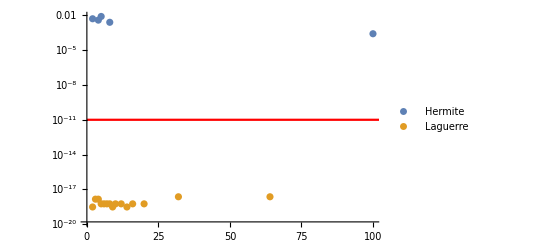

```mathematica
Show[{ListLogPlot[{DELTAHermite,DELTALaguerre},PlotLegends->{"Hermite", "Laguerre"}, PlotRange->All],LogPlot[10^(-11),{x,0,110},PlotStyle->Red]}]
```

```mathematica
ROMBERG TRAPEZIO
```

ROMBERG TRAPEZIO

```mathematica
data =Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_romberg_trap.txt","Table"];
Romberg1 = Take[data,-17][[All,{1,2}]];
Romberg2 = Take[data,-16][[All,{1,3}]];
Romberg3 = Take[data,-15][[All,{1,4}]];
Romberg4 = Take[data,-14][[All,{1,5}]];
Romberg5 = Take[data,-13][[All,{1,6}]];
```

```mathematica
(*lineromb1=FindFit[Romberg1, model,{a,b,c},x]
lineromb2=FindFit[Romberg2, model,{a,b,c},x]
lineromb3=FindFit[Romberg3, model,{a,b,c},x,MaxIterations->1000]*)
```

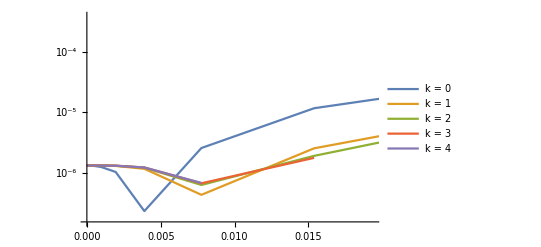

```mathematica
ListLinePlot[{Romberg1,Romberg2,Romberg3,Romberg4,Romberg5},PlotLegends->{"k = 0","k = 1","k = 2","k = 3","k = 4"},PlotRange->Automatic,ScalingFunctions->"Log"]
```

```mathematica
ROMBERG SIMPSON
```

ROMBERG SIMPSON

```mathematica
data =Import["E:\\Alessio\\Desktop\\Computazionale\\es6\\data_romberg_simp.txt","Table"];
Romberg1 = Take[data,-16][[All,{1,2}]];
Romberg2 = Take[data,-15][[All,{1,3}]];
Romberg3 = Take[data,-14][[All,{1,4}]];
Romberg4 = Take[data,-13][[All,{1,5}]];
Romberg5 = Take[data,-12][[All,{1,6}]];
```

```mathematica
(*lineromb1=FindFit[Romberg1, model,{a,b,c},x]
lineromb2=FindFit[Romberg2, model,{a,b,c},x]
lineromb3=FindFit[Romberg3, model,{a,b,c},x,MaxIterations->1000]*)
```

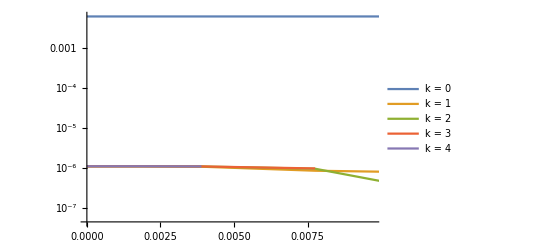

```mathematica
ListLinePlot[{Romberg1,Romberg2,Romberg3,Romberg4,Romberg5},PlotLegends->{"k = 0","k = 1","k = 2","k = 3","k = 4"},PlotRange->Automatic,ScalingFunctions->"Log"]
```

```mathematica
g[x_]= x^5 * Exp[-x^2]
min = 3;
max = Infinity;
```

ⅇ^(-x^2) x^5

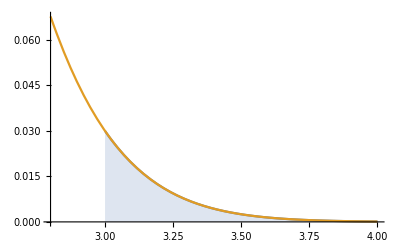

```mathematica
Plot[{If[min<x<max, g[x]],g[x]},{x,min-0.2,4}, Filling->{1->Axis}]
```

```mathematica
Integrate[g[x],{x,3,Infinity}]
N[%]
```

101/(2 ⅇ^9)

0.0062322

```mathematica
f[y_]:=NIntegrate[g[x],{x,2,y}]
```

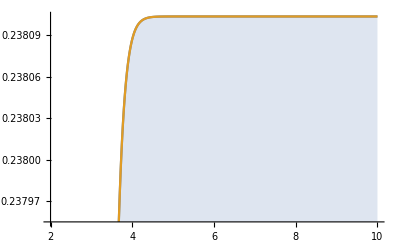

```mathematica
Plot[{If[min<x<max, f[x]],f[x]},{x,min-1,10}, Filling->{1->Axis}]
```

```mathematica
g[x_]= 0.5*(Log[x])^2
min = 0;
max = Exp[-9];
```

0.5 Log[x]^2

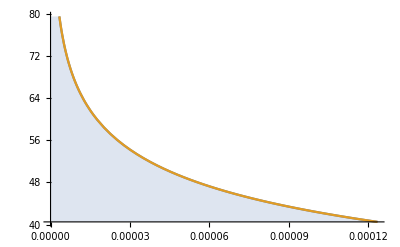

```mathematica
Plot[{If[min<x<max, g[x]],g[x]},{x,min,max }, Filling->{1->Axis}]
```